```mathematica
ρ=ImplicitRegion[t x≥0,{{x,0,1},{t,0,1}}];
η=ImplicitRegion[(t-1)(x-1)≤ 0,{{x,0,1},{t,0,1}}];
ϕ=RegionUnion[ρ,η];
RegionPlot[ϕ]
```

-Graphics-

```mathematica
(*Pick n from a Poisson distribution centered around some mean*)
n=RandomVariate[PoissonDistribution[500]];
(*pick randomly n points from the defined region*)
pt=RandomPoint[ϕ,n];//Timing
pt=Append[pt, {0.5,0}];
Show[RegionPlot[ϕ],Graphics[{PointSize[Small],Point[pt]},Axes->True]]
```

{0.046875,Null}

-Graphics-

```mathematica
{0.03125,Null}
```

{0.03125,Null}

```mathematica
(*Find the causal matrix*)
pt=Sort[pt,#1[[2]]<#2[[2]]&];
c=Table[If[(pt[[i,2]]-pt[[j,2]])^2-(pt[[i,1]]-pt[[j,1]])^2>0,1,0],{i,n},{j,n}];
MatrixForm[c];
Subscript[c, u]=UpperTriangularize[c];
Subscript[Tc, u]=Transpose[Subscript[c, u]];
MatrixForm[Subscript[c, u]];
MatrixForm[Subscript[Tc, u]];
A[a_,b_]:=Length[Intersection[Flatten[SparseArray[Subscript[c, u][[a]]]["NonzeroPositions"]],Flatten[SparseArray[Subscript[Tc, u][[b]]]["NonzeroPositions"]]]];
```

```mathematica
(*Find the link matrix using powers of the causal matrix*)
pathCounts[am_?MatrixQ]:=With[{s=Developer`ToPackedArray@am},FixedPoint[s+#.s&,s,Length[am]]];
l=1-Unitize[pathCounts[Subscript[c, u]]-1];
MatrixForm[l];
```

```mathematica
p0 =Flatten[Position[pt,{0.5,0}]][[1]];
L[p_] := Flatten[SparseArray[l[[p]]]["NonzeroPositions"]];

pairs1 = Permutations[L[p0],{2}];
s=1;
While[s≤ Length[pairs1],
q1=pairs1[[s,1]];
p1=pairs1[[s,2]];
listq2 = Intersection[L[q1],L[p1]];
validq2= Select[listq2,A[p0,#]==2&];
validp2= Select[L[p1],A[p0,#]==1&];
If[Length[validq2]>0 && Length[validp2]>0,
pairs2 = Tuples[{validq2,validp2}];
t=1;
While[t≤ Length[pairs2],
q2=pairs2[[t,1]];
p2=pairs2[[t,2]];
listq3 = Intersection[L[q2],L[p2]];
validq3= Select[listq3,A[p1,#]==2&];
validp3= Select[L[p2],A[p1,#]==1&];
If[Length[validq3]>0 && Length[validp3]>0,
pairs3 = Tuples[{validq3,validp3}];
u=1;
While[u≤ Length[pairs3],
q3=pairs3[[u,1]];
p3=pairs3[[u,2]];
qlist ={q1,q2,q3};
plist = {p1,p2,p3};
u=u+1;
],
qlist ={q1,q2};
plist = {p1,p2};
Break[];
];
t=t+1;
],
qlist ={q1};
plist = {p1};
Break[];
];
s=s+1;
];
```

```mathematica
plist
```

{121}

```mathematica
pairs2 = Tuples[{validq2,validp2}];
t=4;
q2=pairs2[[t,1]];
p2=pairs2[[t,2]];
listq3 = Intersection[L[q2],L[p2]];
validq3= Select[listq3,A[p1,#]==2&]
validp3= Select[L[p2],A[p1,#]==1&]
```

{}

{233}

```mathematica
(*pairs3 = Tuples[{validq3,validp3}];
u=1;
q3=pairs3[[u,1]];
p3=pairs3[[u,2]];
listq4 = Intersection[L[q3],L[p3]];
validq4= Select[listq4,A[p2,#]==2&]
validp4= Select[L[p3],A[p2,#]==1&]*)
```

```mathematica
(*p…list = {}
q…list = {}
pairs1 = Permutations[L[p0],{2}]
s=1;
While[s<=Length[pairs1],
q1=pairs1[[s,1]];
p1=pairs1[[s,2]];
listq2 = Intersection[L[q1],L[p1]];
validq2= Select[listq2,A[p0,#]== 2&];
validp2= Select[L[p1],A[p0,#]== 1&];
pairs2 = Tuples[{validq2,validp2}];
If[Length[pairs2]>0,
t=1;
While[t<=Length[pairs2],
q2=pairs2[[t,1]];
p2=pairs2[[t,2]];
listq3 = Intersection[L[q2],L[p2]];
validq3= Select[listq3,A[p1,#]== 2&];
validp3= Select[L[p2],A[p1,#]== 1&];
If[Length[validq3]>0 && Length[validp3]>0, 
p…list = Append[p…list ,{p1,p2,validp3[[1]]}];
q…list = Append[q…list,{q1,q2,validq3[[1]]}];
Break[];
];
t=t+1;
];
];
s=s+1;
];
p…list
q…list
Graphics[{PointSize[Large],{Point[pt]},{Orange,Point[{pt[[p0]]}]},{Red,Point[{pt[[p1]],pt[[p2]],pt[[validp3[[1]]]]}]},{Green,Point[{pt[[q1]],pt[[q2]],pt[[validq3[[1]]]]}]}},Frame->True,GridLines->Automatic]*)
```

{{22,28},{22,47},{22,61},{28,22},{28,47},{28,61},{47,22},{47,28},{47,61},{61,22},{61,28},{61,47}}

{75}

{83,89,112,189}

{}

{}

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

SparseArray::list: List expected at position 1 in ….

Part::pkspec1: The expression {}⟦1,2⟧ cannot be used as a part specification.

SparseArray::list: List expected at position 1 in ….

Intersection::heads: Heads … and … at positions 2 and 1 are expected to be the same.

Part::partw: Part 83 of {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,«420»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«420»},«48»,«420»}_1 does not exist.

SparseArray::list: List expected at position 1 in SparseArray[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,«420»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«420»},«48»,«420»}_1⟦83⟧].

Part::pkspec1: The expression … cannot be used as a part specification.

SparseArray::list: List expected at position 1 in ….

Intersection::heads: Heads … and SparseArray[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,«420»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«420»},«48»,«420»}_1⟦83⟧] at positions 2 and 1 are expected to be the same.

Part::partw: Part 83 of {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,«420»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«420»},«48»,«420»}_1 does not exist.

SparseArray::list: List expected at position 1 in SparseArray[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,«420»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«420»},«48»,«420»}_1⟦83⟧].

General::stop: Further output of SparseArray::list will be suppressed during this calculation.

Part::pkspec1: The expression … cannot be used as a part specification.

Intersection::heads: Heads … and SparseArray[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,«420»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«420»},«48»,«420»}_1⟦83⟧] at positions 2 and 1 are expected to be the same.

Intersection::heads: Heads … and … at positions 2 and 1 are expected to be the same.

General::stop: Further output of Intersection::heads will be suppressed during this calculation.

SparseArray[{1}⟦{}⟦1,1⟧⟧][NonzeroPositions]∩SparseArray[{1}⟦{}⟦1,2⟧⟧][NonzeroPositions]
 |  |  |  |

Part::pkspec1: The expression {}⟦1,2⟧ cannot be used as a part specification.

SparseArray::list: List expected at position 1 in ….

Part::partw: Part 83 of {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,«420»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«420»},«48»,«420»}_1 does not exist.

SparseArray::list: List expected at position 1 in SparseArray[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,«420»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«420»},«48»,«420»}_1⟦83⟧].

Part::pspec1: Part specification NonzeroPositions is not applicable.

SparseArray::list: List expected at position 1 in SparseArray[Tc_1⟦NonzeroPositions⟧].

General::stop: Further output of SparseArray::list will be suppressed during this calculation.

Intersection::heads: Heads SparseArray[Tc_1⟦NonzeroPositions⟧] and SparseArray[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,«420»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«420»},«48»,«420»}_1⟦83⟧] at positions 2 and 1 are expected to be the same.

SparseArray[{1}⟦{}⟦1,2⟧⟧][]
 |  |  |  |

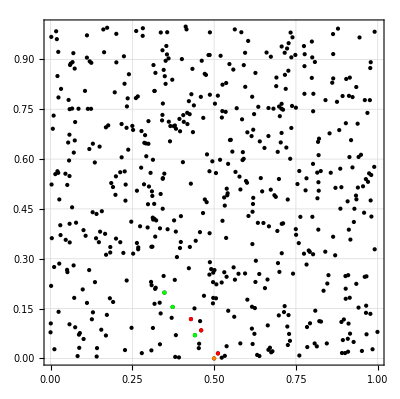

{{17,28},{17,33},{17,36},{17,39},{17,129},{17,165},{17,235},{28,17},{28,33},{28,36},{28,39},{28,129},{28,165},{28,235},{33,17},{33,28},{33,36},{33,39},{33,129},{33,165},{33,235},{36,17},{36,28},{36,33},{36,39},{36,129},{36,165},{36,235},{39,17},{39,28},{39,33},{39,36},{39,129},{39,165},{39,235},{129,17},{129,28},{129,33},{129,36},{129,39},{129,165},{129,235},{165,17},{165,28},{165,33},{165,36},{165,39},{165,129},{165,235},{235,17},{235,28},{235,33},{235,36},{235,39},{235,129},{235,165}}

{17,33,36,36,39,39}

{56,56,64,95,64,95}

{33,17,39,39,36,36}

```mathematica
Graphics[{PointSize[Large],{Point[pt]},{Orange,Point[{pt[[1]]}]},{Red,Point[{pt[[11]],pt[[54]],pt[[73]]}]},{Green,Point[{pt[[44]],pt[[90]],pt[[107]]}]}},Frame->True,GridLines->Automatic]
```

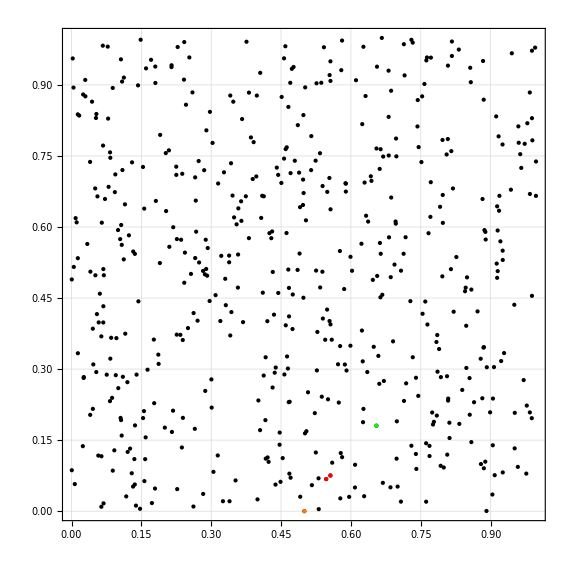

```mathematica
s=4;
Graphics[{PointSize[Large],{Point[pt]},{Orange,Point[{pt[[p0]]}]},{Red,Point[{pt[[p1list[[s]]]],pt[[q1list[[s]]]]}]},{Green,Point[{pt[[q2list[[s]]]]}]}},Frame->True,GridLines->Automatic]
```

Export::chtype: First argument $Failed is not a valid file specification.

$Failed

{{0.72468,0.024655},{0.563696,0.165017}}

{4,20}

{{0.724668,0.024655}}

{{0.563696,0.165017}}

{4}

{20}

4

{{0.615104,0.168327},{0.557824,0.216774}}

{22,27}

{{0.724668,0.024655},{0.615104,0.168327}}

{{0.563696,0.165017},{0.557824,0.216774}}

{4,22}

{20,27}

22

{{0.628916,0.234342},{0.675058,0.250898}}

{29,31}

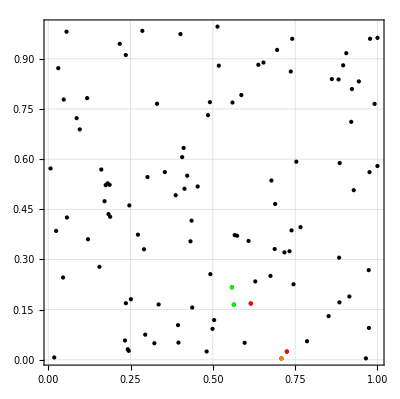

SystemDialogInput::nprmtv: SystemDialogInput is not currently supported within preemptive evaluations.

```mathematica
Export[$Failed,%46,"JPEG"]
```